## Harvest fold - Different noise - Kendall tau

## Setup and Universal Parameters

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/may_harvest_model/multiplicative_noise"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* Figure display parameters *)
aHeadSize=0.03;
indexPos=Scaled[{0.065,1.10}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos={0.035,0.86} ;(* panel letter label *)
imgs=250;
padding={{60,30},{50,40}};
aratio=0.8;
```

## Import Kendall Tau Values

```mathematica
(* Kendall tau values for each type of noise *)
ktauAdd=Import["data_export/ktau_add.csv"];
ktauMulti=Import["data_export/ktau_add.csv"];
ktauR=Import["data_export/ktau_r.csv"];
ktauS=Import["data_export/ktau_s.csv"];
ktauK=Import["data_export/ktau_k.csv"];
```

```mathematica
ktauVals={ktauAdd,ktauMulti,ktauR,ktauS,ktauK};
ktauVals//Dimensions
```

{5,101,7}

```mathematica
(* Column labels *)
ktauK[[1,;;]]
```

{Realisation number,Variance,Standard deviation,Kurtosis,Coefficient of variation,Smax,Lag-1 AC}

```mathematica
(* Noise types *)
noiseTypes={"Add","Multi","r","s","K"};
```

## Box Plots

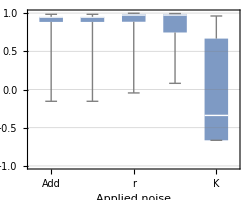

```mathematica
(* Variance *)
index=Position[ktauAdd[[1]],"Variance"][[1,1]];
boxPlotVar=BoxWhiskerChart[ktauVals[[;;,index,2;;]],
PlotRange->{All,{-1,1}},
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
Frame->True,
LabelStyle->14,
ChartStyle->Lighter[TMBcolours[[1]],0.2],
ChartLabels->noiseTypes,
GridLines->{None,Range[-1,1,0.5]},
ImagePadding->padding,
AspectRatio->aratio,
PlotRangeClipping->False,
FrameLabel->{{None,None},{"Applied noise","Variance"}},
FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}}]
```

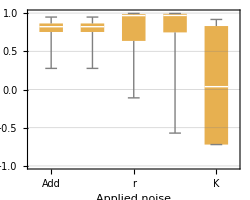

```mathematica
(* CV *)
index=Position[ktauAdd[[1]],"Coefficient of variation"][[1,1]];
boxPlotCV=BoxWhiskerChart[ktauVals[[;;,index,2;;]],
PlotRange->{All,{-1,1}},
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameTicksStyle->{{Directive[FontOpacity->0],Automatic},{Automatic,Automatic}},
ImageSize->imgs,
Frame->True,
LabelStyle->14,
ChartStyle->Lighter[TMBcolours[[2]],0.2],
ChartLabels->noiseTypes,
GridLines->{None,Range[-1,1,0.5]},
ImagePadding->padding,
AspectRatio->aratio,
PlotRangeClipping->False,
FrameLabel->{{None,None},{"Applied noise","CV"}},
FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}}]
```

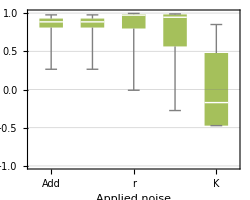

```mathematica
(* lag-1 AC *)
index=Position[ktauAdd[[1]],"Lag-1 AC"][[1,1]];
boxPlotAC=BoxWhiskerChart[ktauVals[[;;,index,2;;]],
PlotRange->{All,{-1,1}},
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameTicksStyle->{{Directive[FontOpacity->0],Automatic},{Automatic,Automatic}},
ImageSize->imgs,
Frame->True,
LabelStyle->14,
ChartStyle->Lighter[TMBcolours[[3]],0.2],
ChartLabels->noiseTypes,
GridLines->{None,Range[-1,1,0.5]},
ImagePadding->padding,
AspectRatio->aratio,
PlotRangeClipping->False,
FrameLabel->{{None,None},{"Applied noise","Lag-1 AC"}},
FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}}]
```

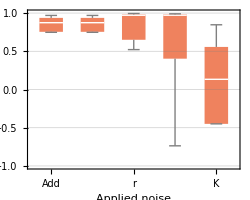

```mathematica
(* Smax *)
index=Position[ktauAdd[[1]],"Smax"][[1,1]];
boxPlotSmax=BoxWhiskerChart[ktauVals[[;;,index,2;;]],
PlotRange->{All,{-1,1}},
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameTicksStyle->{{Directive[FontOpacity->0],Automatic},{Automatic,Automatic}},
ImageSize->imgs,
Frame->True,
LabelStyle->14,
ChartStyle->Lighter[TMBcolours[[4]],0.2],
ChartLabels->noiseTypes,
GridLines->{None,Range[-1,1,0.5]},
ImagePadding->padding,
AspectRatio->aratio,
PlotRangeClipping->False,
FrameLabel->{{None,None},{"Applied noise","S_max"}},
FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}}]
```

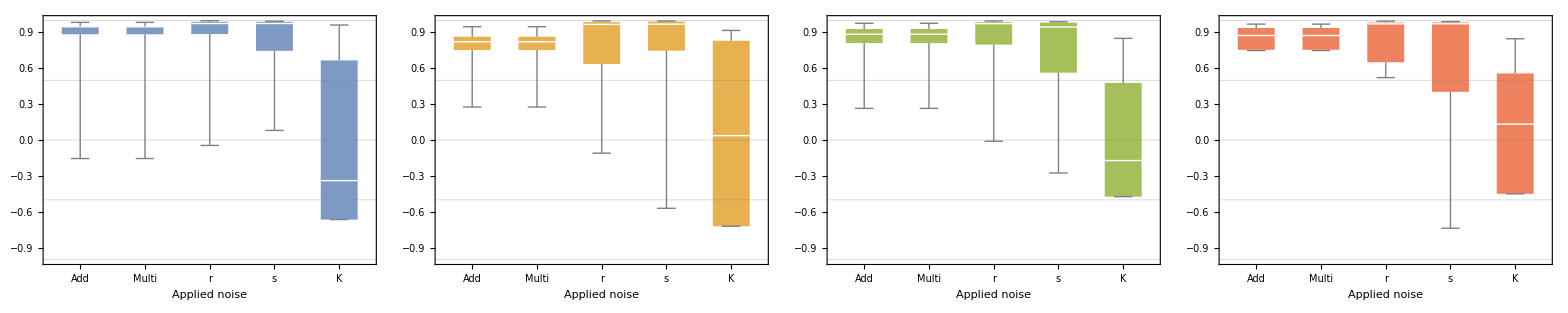

```mathematica
ktauPlot=Grid[{{boxPlotVar,boxPlotCV,boxPlotAC,boxPlotSmax}},Spacings->{-4,0}]
```